# The Movie Database

Source: https://www.themoviedb.org/

## CODE

#### begin package

```mathematica
BeginPackage["TheMovieDatabase`"];
```

```mathematica
ToExpression/@ {"getCertifications","getChanges","getCollection","getCompany","getConfiguration","getCredits","getDiscover","getFind","getGenres","getKeyword","getLists","getMovie","getNetwork","getPerson","getProviders","getReview","getSearch","getTelevision","getTelevisionEpisode","getTelevisionEpisodeGroup","getTelevisionSeason","getTrending"};
```

```mathematica
Begin["Private`"];
```

```mathematica
base="https://api.themoviedb.org/3/";
```

```mathematica
get[url_]:=Module[{request,response},
request=HTTPRequest[URLBuild[url,{"api_key"->SystemCredential["TMDB"]}]];
response=URLRead[request];
Dataset[ImportByteArray[response["BodyByteArray"],"RawJSON"]]
]
```

#### GET /certification/.../list

```mathematica
getCertifications[model:Alternatives["movie","tv"]]:=Module[{url},
url=URLBuild[{base,"certification",model,"list"}];
get[url]
]
```

#### GET /.../changes

```mathematica
getChanges[model:Alternatives["movie","tv","person"]]:=Module[{url},
url=URLBuild[{base,model,"changes"}];
get[url]
]
```

#### GET /collection/{collection_id}

```mathematica
getCollection[id_,Optional[opt:Alternatives["images","translations"],Nothing]]:=Module[{idString,url},
idString=ToString[id];
url=URLBuild[{base,"collection",idString,opt}];
get[url]
]
```

#### GET /company/{company_id}

```mathematica
getCompany[id_,Optional[opt:Alternatives["images","translations"],Nothing]]:=Module[{idString,url},
idString=ToString[id];
url=URLBuild[{base,"company",idString,opt}];
get[url]
]
```

#### GET /configuration

```mathematica
getConfiguration[Optional[opt:Alternatives["countries","jobs","languages","primary_translations","timezones"],Nothing]]:=Module[{url},
url=URLBuild[{base,"configuration",opt}];
get[url]
]
```

#### GET /credit/{credit_id}

```mathematica
getCredits[id_]:=Module[{idString,url},
idString=ToString[id];
url=URLBuild[{base,"credit",idString}];
get[url]
]
```

#### GET /discover/...

complicated search query syntax: https://developers.themoviedb.org/3/discover/movie-discover

```mathematica
getDiscover[model:Alternatives["movie","tv"],query_List]:=Module[{url},
url=URLBuild[{base,"discover",model},query];
get[url]
]
```

#### GET /find/{external_id}

```mathematica
getFind[id_,source:Alternatives["imdb_id","freebase_mid","freebase_id","tvdb_id","tvrage_id","facebook_id","twitter_id","instagram_id"]]:=Module[{idString,url},
idString=ToString[id];
url=URLBuild[{base,"find",idString},{"external_source"->source}];
get[url]
]
```

#### GET /genre/.../list

```mathematica
getGenres[model:Alternatives["movie","tv","person"]]:=Module[{url},
url=URLBuild[{base,"genre",model,"list"}];
get[url]
]
```

#### GET /keyword/{keyword_id}

```mathematica
getKeyword[id_]:=Module[{idString,url},
idString=ToString[id];
url=URLBuild[{base,"keyword",idString}];
get[url]
]
```

#### GET /list/{list_id}

```mathematica
getLists[id_,Optional[opt:"item_status",Nothing]]:=Module[{idString,url},
idString=ToString[id];
url=URLBuild[{base,"list",idString,opt}];
get[url]
]
```

#### GET /movie/{movie_id}

```mathematica
getMovie[m:Alternatives["latest","now_playing","popular","top_rated","upcoming"]]:=Module[{url},
url=URLBuild[{base,"movie",m}];
get[url]]
```

```mathematica
getMovie[id_,Optional[opt:Alternatives["account_states","alternative_titles","changes","credits","external_ids","images","keywords","lists","recommendations","release_dates","reviews","similar","translations","videos","watch/providers"],Nothing]]:=Module[{idString,url},
idString=ToString[id];
url=URLBuild[{base,"movie",idString,opt}];
get[url]
]
```

#### GET /network/{network_id}

```mathematica
getNetwork[id_,Optional[opt:Alternatives["images","alternative_names"],Nothing]]:=Module[{idString,url},
idString=ToString[id];
url=URLBuild[{base,"network",idString,opt}];
get[url]
]
```

#### GET /trending/{media_type}/{time_window}

```mathematica
getTrending[model:Alternatives["all","movie","tv","person"],window:Alternatives["day","week"]]:=Module[{url},
url=URLBuild[{base,"trending",model,window}];
get[url]
]
```

#### GET /person/{person_id}

```mathematica
getPerson[m:Alternatives["latest","popular"]]:=Module[{url},
url=URLBuild[{base,"person",m}];
get[url]]
```

```mathematica
getPerson[id_,Optional[opt:Alternatives["changes","movie_credits","tv_credits","combined_credits","external_ids","images","tagged_images","translations",""],Nothing]]:=Module[{idString,url},
idString=ToString[id];
url=URLBuild[{base,"person",idString,opt}];
get[url]
]
```

#### GET /review/{review_id}

```mathematica
getReview[id_]:=Module[{idString,url},
idString=ToString[id];
url=URLBuild[{base,"review",idString}];
get[url]
]
```

#### GET /search/...

```mathematica
getSearch[model:Alternatives["company","collection","keyword","movie","multi","person","tv"],query_String]:=Module[{url},
url=URLBuild[{base,"search",model},{"query"->query}];
get[url]
]
```

#### GET /tv/{tv_id}

```mathematica
getTelevision[m:Alternatives["latest","airing_today","on_the_air","top_rated","popular"]]:=Module[{url},
url=URLBuild[{base,"tv",m}];
get[url]]
```

```mathematica
getTelevision[id_,Optional[opt:Alternatives["account_states","aggregate_credits","alternative_titles","changes","content_ratings","credits","episode_groups","external_ids","images","keywords","lists","recommendations","release_dates","reviews","screened_theatrically","similar","translations","videos","watch/providers"],Nothing]]:=Module[{idString,url},
idString=ToString[id];
url=URLBuild[{base,"tv",idString,opt}];
get[url]
]
```

#### GET /tv/{tv_id}/season/{season_number}

```mathematica
getTelevisionSeason[tvid_,seasonid_,Optional[opt:Alternatives["account_states","aggregate_credits","changes","credits","external_ids","images","translations","videos"],Nothing]]:=Module[{tvidString,seasonidString,url},
tvidString=ToString[tvid];
seasonidString=ToString[seasonid];
url=URLBuild[{base,"tv",tvidString,"season",seasonidString,opt}];
get[url]
]
```

#### GET /tv/{tv_id}/season/{season_number}/episode/{episode_number}

```mathematica
getTelevisionEpisode[tvid_,seasonid_,episodeid_,Optional[opt:Alternatives["account_states","credits","changes","credits","external_ids","images","translations","videos"],Nothing]]:=Module[{tvidString,seasonidString,episodeidString,url},
tvidString=ToString[tvid];
seasonidString=ToString[seasonid];
episodeidString=ToString[episodeid];
url=URLBuild[{base,"tv",tvidString,"season",seasonidString,"episode",episodeidString,opt}];
get[url]
]
```

#### GET /tv/episode_group/{id}

```mathematica
getTelevisionEpisodeGroup[id_]:=Module[{idString,url},
idString=ToString[id];
url=URLBuild[{base,"tv","episode_group",idString}];
get[url]
]
```

#### GET /watch/providers/regions

```mathematica
getProviders[model:Alternatives["region","movie","tv"]]:=Module[{url},
url=URLBuild[{base,"watch","providers",model}];
get[url]
]
```

#### end package

```mathematica
End[]
```

Private`

```mathematica
EndPackage[]
```

## TEST

#### certifications

```mathematica
ds=getCertifications["movie"]
```

```mathematica
ds["certifications","US"][SortBy[#order&]]
```

```mathematica
getCertifications["tv"]
```

#### changes

```mathematica
getChanges["movie"]
```

```mathematica
getChanges["tv"]
```

#### collections

```mathematica
getCollection[119]
```

```mathematica
getCollection[119,"images"]
```

#### company

```mathematica
getCompany[12]
```

```mathematica
getCompany[12,"images"]
```

#### configuration

```mathematica
getConfiguration[]
```

```mathematica
getConfiguration["countries"]
```

#### credits

```mathematica
getCredits[16]
```

#### discover

```mathematica
(* 2021 movies with Denzel Washington *)
getDiscover["movie",{"primary_release_year"->"2021","with_cast"->"5292","page"->1}]
```

#### find

```mathematica
res=getFind["tt0068646","imdb_id"]
```

#### genres

```mathematica
getGenres["movie"]
```

#### keywords

```mathematica
getKeyword[42]
```

#### lists

```mathematica
getLists[1]
```

#### movie

```mathematica
getMovie["now_playing"]
```

```mathematica
getMovie[120]
```

```mathematica
getMovie[120,"credits"]
```

#### network

```mathematica
getNetwork[1]
```

#### trending

```mathematica
getTrending["movie","day"]
```

#### person

```mathematica
getPerson["popular"]
```

```mathematica
getPerson[1136406]
```

#### review

```mathematica
getReview[123]
```

#### search

```mathematica
getSearch["movie","Lord of the Rings"]
```

```mathematica
getSearch["person","Denzel Washington"]
```

```mathematica
getSearch["tv","Schitt's Creek"]
```

```mathematica
getSearch["company","Paramount"]
```

#### television

```mathematica
getTelevision["on_the_air"]
```

```mathematica
getTelevision[123]
```

#### television season

```mathematica
getTelevisionSeason[123,1]
```

#### television episode

```mathematica
getTelevisionEpisode[123,1,1]
```

#### television episode group

```mathematica
getTelevisionEpisodeGroup[1]
```

#### watch providers

```mathematica
getProviders["movie"]
```

## PLAY

#### Raiders of the Lost Ark

```mathematica
r=getSearch["movie","raiders of the lost ark"];
r["results"]
```

```mathematica
id=r["results",1,"id"]
```

85

```mathematica
m=getMovie[id]
```

```mathematica
Style[m["overview"],"Text"]
```

When Dr. Indiana Jones – the tweed-suited professor who just happens to be a celebrated archaeologist – is hired by the government to locate the legendary Ark of the Covenant, he finds himself up against the entire Nazi regime.

```mathematica
config=getConfiguration[]
```

```mathematica
imageBase=config["images","secure_base_url"]
```

https://image.tmdb.org/t/p/

```mathematica
m["poster_path"]
```

/ceG9VzoRAVGwivFU403Wc3AHRys.jpg

```mathematica
config["images","poster_sizes",5]
```

w500

```mathematica
url=URLBuild[{config["images","secure_base_url"],config["images","poster_sizes",2],m["poster_path"]}];
poster=Import[url]
```

-Graphics-

```mathematica
url=URLBuild[{config["images","secure_base_url"],config["images","backdrop_sizes",2],m["backdrop_path"]}];
backdrop=Import[url]
```

-Graphics-

#### Popular Movies in 2021

discover query syntax: https://developers.themoviedb.org/3/discover/movie-discover

```mathematica
pages=getDiscover["movie",{"primary_release_year"->"2021","sort_by"->"popularity.desc"}]["total_pages"]
```

1362

```mathematica
getDiscover["movie",{"primary_release_year"->"2021","sort_by"->"popularity.desc","page"->1}]
```

```mathematica
datasets=Table[Pause[.25];getDiscover["movie",{"primary_release_year"->"2021","sort_by"->"popularity.desc","page"->page}]["results"],{page,5}];
```

```mathematica
ds=Join@@datasets
```

```mathematica
ids=Normal[ds[All,"id"]]
```

{634649,524434,568124,425909,438695,811592,512195,624860,460458,860623,580489,644495,566525,739413,763788,843241,585245,589761,829358,516329,460465,459151,811072,787310,826749,438631,550988,754934,617653,370172,522402,756403,744275,508943,728526,436969,385128,877183,633802,482321,675445,523936,774741,592508,497698,763148,476669,685274,656991,451048,609972,337404,763164,772436,791373,818192,831223,770254,399566,823610,885110,672582,588228,581726,893941,762433,597208,876716,379686,568620,637649,646380,775943,525660,895001,639721,839436,887767,726684,423108,859041,623135,610253,820511,618162,527774,896221,632357,670429,768744,573164,754067,785538,630004,793967,796499,831827,614917,922017,895006}

```mathematica
Length[ids]
```

100

```mathematica
movies=Map[(Pause[.1];getMovie[#])&,ids];
```

```mathematica
ds2=Dataset[Join[Map[Normal,movies]]]
```

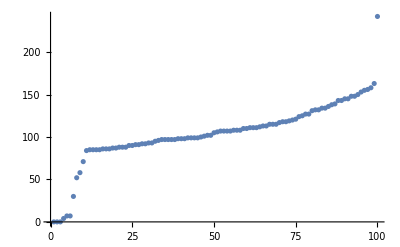

```mathematica
ds2[All,"runtime"]//Normal//Sort//ListPlot
```